```mathematica
gpd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-b-up-xi1-S1.wdx"];
Hdg=Query[1,1]@gpd;
Her=Query[1,2]@gpd;
Hda=Query[1,3]@gpd;
Edg=Query[2,1]@gpd;
Eer=Query[2,2]@gpd;
Eda=Query[2,3]@gpd;
Hdgf=Interpolation[Flatten[Hdg,1]];
Herf=Interpolation[Flatten[Her,1]];
Hdaf=Interpolation[Flatten[Hda,1]];
Edgf=Interpolation[Flatten[Edg,1]];
Eerf=Interpolation[Flatten[Eer,1]];
Edaf=Interpolation[Flatten[Eda,1]];
```

```mathematica
Hdgf1[x_,t_]:=Chop[Hdgf[x,t],10^-8];
Herf1[x_,t_]:=Chop[Herf[x,t],10^-8]+Chop[Hdaf[x,t],10^-8];
Edgf1[x_,t_]:=Chop[Edgf[x,t],10^-8];
Eerf1[x_,t_]:=Chop[Eerf[x,t],10^-8]+Chop[Edaf[x,t],10^-8];
```

```mathematica
pH=Show[Plot3D[-I*Hdgf1[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Herf1[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","H^d(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
Plot3D[-I*t1[x,t],{x,-0.1,0.1},{t,-1,-0.037},PlotRange->All]
```

-Graphics3D-

```mathematica
t1[x_,t_]=Chop[Herf[x,t],10^-6];
```

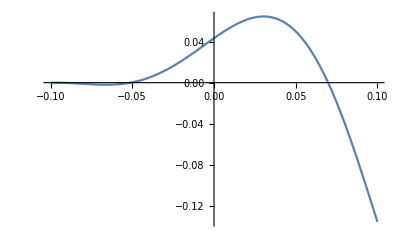

```mathematica
Plot[Re[-I*t1[x,-0.037]],{x,-0.1,0.1}]
```

```mathematica
t1[0,-0.037]
```

0.+0.0431951 ⅈ

```mathematica
pE=Show[Plot3D[-I*Edgf1[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Eerf1[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","E^d(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-